# Math 223: Homework 5

Maia Powell

25 February 2021

For this homework, we will be using the method of dominant balance to determine the leading behaviors of solutions of nonhomogeneous differential equations and computing the asymptotic behavior of integrals.

## Problem 1

#### Find the first three terms in the local behavior as x → 0^+ of a particular solution y(x) to y'+xy=x^-3.

```mathematica
AsymptoticDSolveValue[y'[x]+x y[x]==x^-3,y[x],{x,0,1}]
```

(1-x^2/2) C[1]+(1-x^2/2) (-1/(2 x^2)+x^2/8+Log[x]/2)

```mathematica
Series[(1-x^2/2) (-1/(2 x^2)+x^2/8+Log[x]/2),{x,0,1}]
```

-1/(2 x^2)+1/4 (1+2 Log[x])+O[x]^2

Solving the homogeneous equation to find y

```mathematica
DSolve[y'[x]+x y[x]==0,y[x],{x,0,1}]
```

{{y[x]→ⅇ^(-x^2/2) C[1]}}

Obtaining y’ for our assumptions

```mathematica
D[DSolve[y'[x]+x y[x]==0,y[x],{x,0,1}], x]
```

{{y'[x]→-ⅇ^(-x^2/2) x C[1]}}

Checking that x^-3 << xy (implying that y ~ -xy):

```mathematica
Limit[x^-3/(x ⅇ^(-x^2/2)),x->0]
```

∞

Checking that y' << x^-3 (implying that xy ~ x^-3 → y ~ x^-4):

```mathematica
Limit[D[x^-4, x]/x^-3,x->0]
```

-∞

Checking that  xy << x^-3 (implying that y' ~ x^-3):

```mathematica
DSolve[y'[x]-x^-3== 0, y[x], {x, 0, 1}]
```

{{y[x]→-1/(2 x^2)+C[1]}}

```mathematica
Limit[(x*(-1/(2 x^2)))/x^-3,x->0]
```

0

yields the leading behavior y(x) ∼ -1/2 x^-2 as x→0.

To compute a correction, we substitute y(x) = -1/2 x^-2+c(x), c(x) ≪x^-2 as x→0.

```mathematica
y'[x]+x y[x]==x^-3 /. y -> Function[x,-1/2 x^-2+c[x]]//FullSimplify
```

2 (x c[x]+c'[x])==1/x

We now assume x c ≪ 1/2 x^-1 as x→0. This leads to the asymptotic relation c'~ 1/2 x^-1 as x→0.

```mathematica
DSolve[c'[x]-1/2 x^-1== 0, c[x], {x, 0, 1}]
```

{{c[x]→C[1]+Log[x]/2}}

When then check to confirm that our assumption is satisfied, and find that it is!

```mathematica
Limit[(x*(Log[x]/2))/(1/2 x^-1),x->0]
```

0

Thus, c(x) ∼ Log[x]/2 as x→0 and consequently, y(x) ∼ -1/2 x^-2+Log[x]/2 as x→0.

To compute another correction, we substitute y(x) = -1/2 x^-2+Log[x]/2+ d(x) as x→0.

```mathematica
y'[x]+x y[x]==x^-3 /. y -> Function[x,-1/2 x^-2+Log[x]/2+ d[x]]//FullSimplify // Expand
```

2 x d[x]+x Log[x]+2 d'[x]==0

We now assume d(x) << c(x) → d(x) << (log(x))/2 → 2xd(x) << xlog(x)  as x→0. This leads to the asymptotic relation d'(x) ~ (-xlog(x))/2 as x→0.

```mathematica
DSolve[d'[x]+ x*Log[x]*1/2== 0, d[x], {x, 0, 1}] // FullSimplify // Expand
```

{{d[x]→x^2/8+C[1]-1/4 x^2 Log[x]}}

When then check to confirm that our assumption is satisfied, and find that it is!

```mathematica
Limit[(x^2/8+C[1]-1/4 x^2 Log[x])/(Log[x]/2),x->0]
```

0

Thus, d(x) ∼ x^2/8-1/4 x^2 Log[x] as x→0 and consequently, y(x) ∼ -1/2 x^-2+Log[x]/2+1/8 x^2-1/4 x^2 Log[x] as x→0.

## Problem 2

#### Find the leading behavior of (∫_0)^1 e^-xt/(1+t^2)dt as x → 0^+.

Let’s expand the function to be integrated about x = 0.

```mathematica
Series[Exp[-x*t]/(1+t^2), {x, 0, 2}]
```

1/(1+t^2)-(t x)/(1+t^2)+(t^2 x^2)/(2 (1+t^2))+O[x]^3

We then integrate this Series to obtain the leading behavior:

```mathematica
approx = Integrate[ Collect[Series[Exp[-x*t]/(1+t^2), {x, 0, 2}],x],{t,0,1}] // FullSimplify  // Expand
```

π/4+x^2/2-(π x^2)/8-1/2 x Log[2]

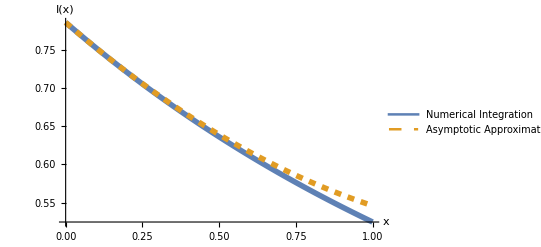

```mathematica
Plot[{NIntegrate[Exp[-x*t]/(1+t^2),{t,0,1}],approx},{x,0,1},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Numerical Integration", "Asymptotic Approximation"}]
```

## Problem 3

#### Find the asymptotic series for (∫_0)^x t^(-1/4)e^-t dt as x → 0^+.

We first perform Integration by Parts: (∫_0)^x t^(-1/4)e^-t dt
u = e^-t, dv = t^(-1/4)dt  → du = -e^-tdt , v = (4 t^(3/4))/3 
(∫_0)^x t^(-1/4)e^-t dt  = ( e^-t)((4 t^(3/4))/3)(|^x)_0 + (∫_0)^x((4 t^(3/4))/3)( e^-t)dt
= ( e^-x)((4 x^(3/4))/3)- ( e^0)((4 0^(3/4))/3) + (∫_0)^x((4 t^(3/4))/3)( e^-t)dt
= (4 x^(3/4))/(3 e^x)+ (∫_0)^x((4 t^(3/4))/3)( e^-t)dt

Performing Integration by Parts once again: 
(4 x^(3/4))/(3 e^x)+ 4/3(∫_0)^x(t^(3/4))( e^-t)dt
u = e^-t, dv = t^(3/4)dt  → du = -e^-tdt , v =4/7 t^(7/4)  
(4 x^(3/4))/(3 e^x)+ 4/3(∫_0)^x(t^(3/4))( e^-t)dt = (4 x^(3/4))/(3 e^x)+ 4/3(e^-t 4/7 t^(7/4)(|^x)_0+(∫_0)^x e^-t 4/7 t^(7/4)dt) 
= (4 x^(3/4))/(3 e^x)+ 4/3(e^-x 4/7 x^(7/4)+(∫_0)^x e^-t 4/7 t^(7/4)dt)
= (4 x^(3/4))/(3 e^x)+ 16/21(x^(7/4)/e^x+(∫_0)^x e^-t t^(7/4)dt)
= (4 x^(3/4))/(3 e^x)+ 16/21 x^(7/4)/e^x+16/21(∫_0)^x e^-t t^(7/4)dt

We thus approximate the solution using (4 x^(3/4))/(3 e^x)+ 16/21 x^(7/4)/e^x.

We additionally can compute a series approximation:

```mathematica
Integrate[ Collect[Series[(4 s^2)*Exp[-s^4],{s,0,6}],s],{s,0, x^(1/4)}]
```

(4 x^(3/4))/3-(4 x^(7/4))/7

Finally, we obtain a Numerical Integration for comparison (with the Series approximation and approximation obtained using Integration by Parts) via plot:

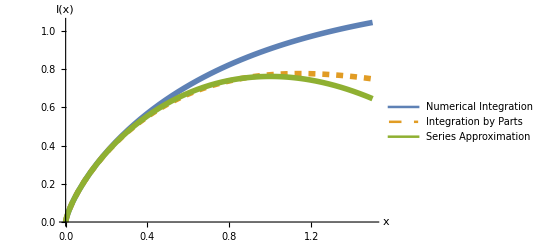

```mathematica
Plot[{NIntegrate[t^(-1/4)Exp[-t],{t,0,x}],(4 x^(3/4))/(3Exp[x])+ 16/21 x^(7/4)/Exp[x],Integrate[ Collect[Series[(4 s^2)*Exp[-s^4],{s,0,6}],s],{s,0, x^(1/4)}]},{x,0,1.5},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Numerical Integration","Integration by Parts", "Series Approximation"}]
```